# Top Quark Signal

## Analytic angular coefficients and mass dependence

## 1. Conventions and scalar soft-loop seeds

The target is the five complex angular coefficients in SMS in CHC, Eq. (59). nu = mt/H > 0. All results below use the positive soft branch and the phase convention 16^(2 I nu) in Eq. (58). Nc, gt and the overall momentum/H factors in Eq. (57) are excluded. Outputs and native Mathematica plots are saved in this notebook; no external files are needed to inspect or reevaluate it. Evaluate from the beginning in a fresh kernel.

```mathematica
BeginPackage["TopQuarkSignal`"];ClearAll["TopQuarkSignal`*"];
```

```mathematica
wp=50;massMin=1/10;massMax=5;assumptionsTop=nu>0;formTop[expr_]:=TraditionalForm@@{expr};nu/:MakeBoxes[nu,TraditionalForm]:="ν";pp1/:MakeBoxes[pp1,TraditionalForm]:=SubscriptBox["P","1"];pp2/:MakeBoxes[pp2,TraditionalForm]:=SubscriptBox["P","2"];q00/:MakeBoxes[q00,TraditionalForm]:=SubscriptBox["Q","00"];tGamma/:MakeBoxes[tGamma,TraditionalForm]:="T";eEndpoint/:MakeBoxes[eEndpoint,TraditionalForm]:="E";bb/:MakeBoxes[bb,TraditionalForm]:="ℬ";gSymbol/:MakeBoxes[gSymbol,TraditionalForm]:="𝒢";
```

Exact rational constants are retained until numerical evaluation. FullSimplify is applied with explicit assumptions and a finite search time; its output need not be a unique shortest form. I and D retain their built-in Mathematica meanings. softBTop denotes the common factor in Eq. (119); BTop denotes the angular coefficient.

```mathematica
f0Top[alpha_,beta_]:=(Gamma[alpha+beta-3/2] Gamma[3/2-alpha] Gamma[3/2-beta])/(Gamma[3-alpha-beta] Gamma[alpha] Gamma[beta]);rhoTop[v_]:=1/2-ⅈ v;gTop[v_]:=f0Top[rhoTop[v],rhoTop[v]]/(4 π)^(3/2);cPlusTop[v_]:=(2^(-1-2 ⅈ v) Gamma[1/2-ⅈ v]^2)/π;{{"rho(nu)", formTop[rhoTop[nu]]}, {"f0(alpha,beta)", formTop[f0Top[alpha,beta]]}, {"c+(nu)", formTop[cPlusTop[nu]]}}
```

rho(nu) | 1/2-ⅈ ν
f0(alpha,beta) | (3/2-alpha 3/2-beta alpha+beta-3/2)/(alpha beta -alpha-beta+3)
c+(nu) | (2^(-1-2 ⅈ ν) (1/2-ⅈ ν)^2)/π

f0 is the analytically continued convolution of Sec. 2.1. Its definition excludes (4 Pi)^(3/2). The first saved simplification is the common Gamma factor Gtop in Eq. (108).

```mathematica
gTopSimp=FullSimplify[gTop[nu],assumptionsTop,TimeConstraint->8];formTop[gTopSimp]
```

-(2^(-3-4 ⅈ ν) cosh^2(π ν) -2 ⅈ ν-1/2 2 ⅈ ν+2)/(π^(5/2) (-2 ν+ⅈ)^2)

```mathematica
gTopPaper[v_]:=(Gamma[-1/2-2 ⅈ v] Gamma[1+ⅈ v]^2)/((4 π)^(3/2) Gamma[2+2 ⅈ v] Gamma[1/2-ⅈ v]^2);softGammaCheck=FullSimplify[gTop[nu]-gTopPaper[nu],assumptionsTop];softGammaCheck
```

0

### Scalar moments and Gamma recurrence

```mathematica
frTop[ell_Integer,alpha_,beta_]:=∑_(u=0)^ell ∑_(v=0)^(ell-u) (ell! (-1)^(ell-u) f0Top[alpha+ell/2-v,beta-u])/(2^ell u! v! (ell-u-v)!);jTop[ell_Integer,m_Integer,n_Integer,x_]:=frTop[ell,x-m/2,x+n/2];shiftRatioTop[j_Integer,k_Integer,rho_]:=(Pochhammer[3/2-rho,j] Pochhammer[3/2-rho,k] Pochhammer[1-rho,j] Pochhammer[1-rho,k])/(Pochhammer[5/2-2 rho,j+k] Pochhammer[3-2 rho,j+k]);jRatioTop[ell_Integer,m_Integer,v_]:=∑_(u=0)^ell ∑_(w=0)^(ell-u) (ell! (-1)^(ell-u) shiftRatioTop[1/2 (m+1-ell)+w,u,rhoTop[v]])/(2^ell u! w! (ell-u-w)!);
```

shiftRatioTop(j,k,rho) = f0(rho-j,rho-k)/f0(rho,rho), obtained by Gamma recurrence. jRatioTop is J_ell(m,1;-I nu)/f0(rho,rho) for the integer shifts used below. This extracts the common Gamma factor before FullSimplify, leaving rational algebra.

## 2. Soft-loop coefficients I11, I12, I21 and I22

Eq. (107) is reduced in the basis {1, S, TB, TD}, where S = cos(theta1)^2 + cos(theta3)^2 - 3 cos(theta1)^2 cos(theta3)^2, TB = sin(2 theta1) sin(2 theta3) cos(phi3), TD = sin(theta1)^2 sin(theta3)^2 cos(2 phi3). The following five entries are I12 and the four components of I22, divided by Gtop.

```mathematica
loopJExpressions={1/2 (jSym[0,3]-jSym[2,3]+jSym[1,2]-jSym[3,2])+1/4 (jSym[0,1]-jSym[2,1]),1/4 (2 jSym[4,3]-3 jSym[2,3]+jSym[0,3]+jSym[3,2]-jSym[1,2]),1/4 (-6 jSym[4,3]+7 jSym[2,3]-jSym[0,3]+5 jSym[1,2]-5 jSym[3,2]+jSym[0,1]-jSym[2,1]),1/16 (-16 jSym[4,3]+14 jSym[2,3]-2 jSym[0,3]+10 jSym[1,2]-18 jSym[3,2]+2 jSym[0,1]-7 jSym[2,1]-jSym[1,0]),1/4 (jSym[4,3]-jSym[2,3]+jSym[3,2]-jSym[1,2])};loopRatios=Factor/@FullSimplify[loopJExpressions/.jSym[ell_,m_]:>jRatioTop[ell,m,nu],assumptionsTop,TimeConstraint->12];Grid[MapThread[{#1,formTop[#2]}&,{{"I12/G","I22: constant/G","I22: S/G","I22: TB/G","I22: TD/G"},loopRatios}],Frame->All,Alignment->Left]
```

I12/G | ((ν-ⅈ) (2 ν-ⅈ))/(4 (-5-4 ⅈ ν) (2 ν-3 ⅈ) (4 ν-3 ⅈ))
I22: constant/G | ((ν-ⅈ) (ν-2 ⅈ) (2 ν-ⅈ))/(4 (-5-4 ⅈ ν) (2 ν-3 ⅈ) (2 ν-5 ⅈ) (4 ν-3 ⅈ))
I22: S/G | -(ⅈ (ν-ⅈ)^2 (2 ν-ⅈ))/(4 (2 ν-3 ⅈ) (2 ν-5 ⅈ) (4 ν-3 ⅈ) (4 ν-5 ⅈ))
I22: TB/G | -(ⅈ (ν-ⅈ) (2 ν-ⅈ))/(8 (2 ν-5 ⅈ) (4 ν-3 ⅈ) (4 ν-5 ⅈ))
I22: TD/G | ((ν-ⅈ) (ν-2 ⅈ))/(4 (-5-4 ⅈ ν) (2 ν-5 ⅈ) (4 ν-3 ⅈ))

```mathematica
loopCommon=-(1+ⅈ nu)/(4 (5+2 ⅈ nu) (3+2 ⅈ nu) (5+4 ⅈ nu) (3+4 ⅈ nu));loopPaperRatios={-((1+ⅈ nu) (1+2 ⅈ nu))/(4 (3+2 ⅈ nu) (5+4 ⅈ nu) (3+4 ⅈ nu)),loopCommon (2+ⅈ nu) (1+2 ⅈ nu),-loopCommon (1+ⅈ nu) (1+2 ⅈ nu),1/2 (-loopCommon) (1+2 ⅈ nu) (3+2 ⅈ nu),loopCommon (2+ⅈ nu) (3+2 ⅈ nu)};loopSymbolicCheck=FullSimplify[loopRatios-loopPaperRatios,assumptionsTop];loopSymbolicCheck
```

{0,0,0,0,0}

```mathematica
i12Top[v_]:=gTop[v] (loopRatios⟦1⟧/.nu->v);i11Top[v_]:=3 i12Top[v];i21Top[v_]:=i12Top[v];i22Top[v_,t1_,t3_,ph_]:=gTop[v] (Rest[loopRatios]/.nu->v).{1,Cos[t1]^2+Cos[t3]^2-3 Cos[t1]^2 Cos[t3]^2,Sin[2 t1] Sin[2 t3] Cos[ph],Sin[t1]^2 Sin[t3]^2 Cos[2 ph]};formTop[gSymbol Rest[loopRatios].{1,sAngular,bAngular,dAngular}]
```

𝒢 (-(ⅈ bAngular (2 ν-ⅈ) (ν-ⅈ))/(8 (2 ν-5 ⅈ) (4 ν-3 ⅈ) (4 ν-5 ⅈ))+(dAngular (ν-2 ⅈ) (ν-ⅈ))/(4 (-5-4 ⅈ ν) (2 ν-5 ⅈ) (4 ν-3 ⅈ))+((ν-2 ⅈ) (2 ν-ⅈ) (ν-ⅈ))/(4 (-5-4 ⅈ ν) (2 ν-3 ⅈ) (2 ν-5 ⅈ) (4 ν-3 ⅈ))-(ⅈ (2 ν-ⅈ) (ν-ⅈ)^2 sAngular)/(4 (2 ν-3 ⅈ) (2 ν-5 ⅈ) (4 ν-3 ⅈ) (4 ν-5 ⅈ)))

In the displayed I22 expression, gSymbol = Gtop(nu), sAngular = S, bAngular = TB and dAngular = TD. The functions above retain the full angles. The next check independently evaluates the original shifted Gamma sums, without the recurrence reduction.

```mathematica
loopNumericChecks=Table[Module[{direct,reduced},direct=N[(loopJExpressions/.jSym[ell_,m_]:>jTop[ell,m,1,-ⅈ v])/(4 π)^(3/2),50];reduced=N[gTop[v] (loopRatios/.nu->v),50];{v,Max[Abs[(direct-reduced)/reduced]]}],{v,{1/5,73/100,2,5}}];Grid[Prepend[N[loopNumericChecks,6],{"mt/H","max relative Gamma-sum residual"}],Frame->All]
```

mt/H | max relative Gamma-sum residual
0.2 | 0.
0.73 | 0.
2. | 0.
5. | 0.

## 3. Whittaker seeds and regulated hard integrals

Eqs. (112)-(118). kappa = +/-1/2, a,b = +/-1. kOppTop and kSameTop use the regularized 3F2; this differs from the ordinary 3F2 used later in QTop. The integral definition fixes all phases. The finite part is taken only after the full SK and kappa combinations have been assembled.

```mathematica
kOppTop[a_,p_,q_,v_,kap_]:=(Exp[1/2 (-ⅈ) a π (p-q)+ⅈ π kap] 2^(-3-p-q) Gamma[3/2+p-ⅈ v] Gamma[3/2+p+ⅈ v] Gamma[3/2+q-ⅈ v] Gamma[3/2+q+ⅈ v])/(Gamma[2+p+a kap] Gamma[2+q-a kap]);kSameTop[a_,p_,q_,v_,kap_]:=-a ⅈ Exp[1/2 (-ⅈ) a π (p+q)] 2^(-3-p-q) Gamma[3/2+p+a ⅈ v] Gamma[3/2+q+a ⅈ v] (((Exp[2 ⅈ π kap]+Exp[-2 π v]) Gamma[3/2+p-a ⅈ v] Gamma[3/2+q-a ⅈ v] Gamma[1/2+a kap-ⅈ v] Gamma[1/2+a kap+ⅈ v])/((2 π) (Gamma[2+p+a kap] Gamma[2+q+a kap]))+a ⅈ Gamma[3+p+q] HypergeometricPFQRegularized[{3+p+q,1/2-a kap+a ⅈ v,1},{5/2+p+a ⅈ v,5/2+q+a ⅈ v},1]);kSeedTop[a_,b_,p_,q_,v_,kap_]:=If[a==b,kSameTop[a,p,q,v,kap],kOppTop[a,p,q,v,kap]];
```

The symbolic H0 and H1 definitions below retain KTop(a,b,kappa,p,q,r,nu) as an unevaluated seed at u=2r/(1+r). At r=1 it is kSeedTop. For the radial derivative, Eq. (117) shifts p or q; the explicit powers of r and the (a +/- r)/r factors must also be differentiated.

```mathematica
h0FormalTop[q1_,q2_,r_,v_]:=1/2 (-ⅈ) Sum[With[{p=q1-3/2+m,q=q2-3/2+n},(ⅈ a)^m (ⅈ b)^n r^(-3-p-q) ((p+3/2+ⅈ v) (KTop[a,b,-1/2,p,q,r,v]-KTop[a,b,1/2,p,q,r,v])+(ⅈ (a-r) KTop[a,b,1/2,p+1,q,r,v])/r-(ⅈ (a+r) KTop[a,b,-1/2,p+1,q,r,v])/r)],{a,{-1,1}},{b,{-1,1}},{m,0,1},{n,0,1}];h1FormalTop[q1_,q2_,r_,v_]:=1/2 (-ⅈ) Sum[With[{p=q1-3/2+m,q=q2-3/2+n},(ⅈ a)^m (ⅈ b)^n r^(-3-p-q) ((p+3/2-ⅈ v) (KTop[a,b,-1/2,p,q,r,v]+KTop[a,b,1/2,p,q,r,v])-(ⅈ (a-r) KTop[a,b,1/2,p+1,q,r,v])/r-(ⅈ (a+r) KTop[a,b,-1/2,p+1,q,r,v])/r)],{a,{-1,1}},{b,{-1,1}},{m,0,1},{n,0,1}];{P1[nu]==FinitePart[H0[ⅈ nu+delta,ⅈ nu+delta,1,nu]+(2 ⅈ H1[1+ⅈ nu+delta,ⅈ nu+delta,1,nu])/(1+2 ⅈ nu),delta,0],P2[nu]==FinitePart[D[H0[ⅈ nu+delta,ⅈ nu+delta,r,nu], r]-H0[ⅈ nu+delta,ⅈ nu+delta,r,nu]/.r->1,delta,0]}
```

{P1[nu]==FinitePart[H0[ⅈ nu+delta,ⅈ nu+delta,1,nu]+(2 ⅈ H1[1+ⅈ nu+delta,ⅈ nu+delta,1,nu])/(1+2 ⅈ nu),delta,0],P2[nu]==FinitePart[∂_r H0[ⅈ nu+delta,ⅈ nu+delta,r,nu]-H0[ⅈ nu+delta,ⅈ nu+delta,r,nu]/.r→1,delta,0]}

### Stable numerical evaluation of the regulated definitions

For the independent regulator check, a Thomae transformation is used when it improves the convergence balance of 3F2(1). The representation has the same analytic continuation as the regularized seed. The numerical seed cache includes working precision. The derivative is implemented directly using Eq. (117).

```mathematica
hyper3RegN[upper_List,lower_List,prec_Integer]:=Module[{aa=N[upper,prec],bb=N[lower,prec],balance,choices,best,ii,jj,c,pair,d,e},balance=Total[bb]-Total[aa];choices=Join[{{Re[balance],0,0}},Flatten[Table[{Re[bb⟦j⟧-aa⟦i⟧],i,j},{i,3},{j,2}],1]];best=First[MaximalBy[choices,First]];If[best⟦2⟧==0,Return[N[HypergeometricPFQRegularized[aa,bb,1],prec]]];{ii,jj}=Rest[best];c=aa⟦ii⟧;pair=Delete[aa,ii];e=bb⟦jj⟧;d=bb⟦3-jj⟧;N[(Gamma[balance] HypergeometricPFQ[{d-pair⟦1⟧,d-pair⟦2⟧,c},{d,balance+c},1])/(Gamma[e-c] Gamma[balance+c] Gamma[d]),prec]];kSeedN[a_Integer,b_Integer,p_?NumericQ,q_?NumericQ,v_?NumericQ,kap_,prec_Integer]:=kSeedN[a,b,p,q,v,kap,prec]=Module[{pp=N[p,prec],qq=N[q,prec],vv=N[v,prec],kk=N[kap,prec],base,hom,part},If[a≠b,Return[N[kOppTop[a,pp,qq,vv,kk],prec]]];base=-a ⅈ Exp[1/2 (-ⅈ) a π (pp+qq)] 2^(-3-pp-qq) Gamma[3/2+pp+a ⅈ vv] Gamma[3/2+qq+a ⅈ vv];hom=((Exp[2 ⅈ π kk]+Exp[-2 π vv]) Gamma[3/2+pp-a ⅈ vv] Gamma[3/2+qq-a ⅈ vv] Gamma[1/2+a kk-ⅈ vv] Gamma[1/2+a kk+ⅈ vv])/((2 π) (Gamma[2+pp+a kk] Gamma[2+qq+a kk]));part=a ⅈ Gamma[3+pp+qq] hyper3RegN[{3+pp+qq,1/2-a kk+a ⅈ vv,1},{5/2+pp+a ⅈ vv,5/2+qq+a ⅈ vv},prec];N[base (hom+part),prec]];kSeedDrN[a_,b_,p_,q_,v_,kap_,prec_]:=ⅈ a kSeedN[a,b,p+1,q,v,kap,prec]+ⅈ b kSeedN[a,b,p,q+1,v,kap,prec];
```

```mathematica
hardMomentsN[v_?NumericQ,q1_?NumericQ,q2_?NumericQ,prec_Integer]:=Module[{h0=0,h1=0,dh0=0,p,q,kp,km,kps,kms,dkp,dkm,dkps,dkms,w,t0,t1,dt0},Do[p=q1-3/2+m;q=q2-3/2+n;w=1/2 (-ⅈ) (ⅈ a)^m (ⅈ b)^n;kp=kSeedN[a,b,p,q,v,1/2,prec];km=kSeedN[a,b,p,q,v,-1/2,prec];kps=kSeedN[a,b,p+1,q,v,1/2,prec];kms=kSeedN[a,b,p+1,q,v,-1/2,prec];dkp=kSeedDrN[a,b,p,q,v,1/2,prec];dkm=kSeedDrN[a,b,p,q,v,-1/2,prec];dkps=kSeedDrN[a,b,p+1,q,v,1/2,prec];dkms=kSeedDrN[a,b,p+1,q,v,-1/2,prec];t0=(p+3/2+ⅈ v) (km-kp)+ⅈ (a-1) kps-ⅈ (a+1) kms;t1=(p+3/2-ⅈ v) (km+kp)-ⅈ (a-1) kps-ⅈ (a+1) kms;dt0=-(3+p+q) t0+(p+3/2+ⅈ v) (dkm-dkp)+ⅈ (a-1) dkps-ⅈ (a+1) dkms-ⅈ a kps+ⅈ a kms;h0+=w t0;h1+=w t1;dh0+=w dt0,{a,{-1,1}},{b,{-1,1}},{m,0,1},{n,0,1}];N[{h0,h1,dh0},prec]];regulatedHardTop[v_?NumericQ,del_?NumericQ,prec_Integer:50]:=regulatedHardTop[v,del,prec]=Module[{base,shift},base=hardMomentsN[v,ⅈ v+del,ⅈ v+del,prec];shift=hardMomentsN[v,1+ⅈ v+del,ⅈ v+del,prec];{base⟦1⟧+(2 ⅈ shift⟦2⟧)/(1+2 ⅈ v),base⟦3⟧-base⟦1⟧,base⟦1⟧,shift⟦2⟧}];regulatorLimitTop[v_,step_,levels_Integer,prec_Integer:50]:=Module[{vals},vals=Table[regulatedHardTop[v,step/2^j,prec],{j,0,levels-1}];Do[vals=Table[(2^ord vals⟦j+1⟧-vals⟦j⟧)/(2^ord-1),{j,Length[vals]-1}],{ord,1,levels-1}];First[vals]];
```

## 4. Finite analytic hard coefficients and FullSimplify results

A finite representation of the assembled Eq. (118) is expressed through Q_mn. This representation is also present in the source manuscript comments and the existing Whittaker calculation. Its equivalence to the regulated definition is checked numerically below; that check is distinct from a symbolic proof of the regulator limit. Q_mn contains an ordinary 3F2 with convergence balance 1 + I nu. Only Q00 remains nontrivial after the other four functions are reduced.

```mathematica
qTop[m_,n_,v_]:=(2^(-1-2 ⅈ v-m-n) Gamma[1+2 ⅈ v+m+n] HypergeometricPFQ[{1+2 ⅈ v+m+n,1+ⅈ v,1},{2+2 ⅈ v+m,2+2 ⅈ v+n},1])/((1+2 ⅈ v+m) (1+2 ⅈ v+n));timeGammaTop[v_]:=2^(-1-2 ⅈ v) Gamma[1+2 ⅈ v];endpointTop[v_]:=π^2 2^(-1-2 ⅈ v) (Gamma[1+2 ⅈ v]/Gamma[1+ⅈ v])^2;formTop[qTop[0,0,nu]]
```

(2^(-1-2 ⅈ ν) 2 ⅈ ν+1 _3 F_2(1,ⅈ ν+1,2 ⅈ ν+1;2 ⅈ ν+2,2 ⅈ ν+2;1))/(1+2 ⅈ ν)^2

```mathematica
qPairs={{0,1},{1,1},{0,2},{1,2}};qRatioSimp=FullSimplify[Table[qTop[pair⟦1⟧,pair⟦2⟧,nu]/timeGammaTop[nu],{pair,qPairs}],assumptionsTop,TimeConstraint->12];Grid[MapThread[{#1,formTop[#2]}&,{{"Q01/T","Q11/T","Q02/T","Q12/T"},qRatioSimp}],Frame->All,Alignment->Left]
```

Q01/T | 1/(2 (1+ⅈ ν))
Q11/T | 1/2+ⅈ/(4 (ν-ⅈ))
Q02/T | 1/2+ⅈ/(4 (ν-2 ⅈ))
Q12/T | 1/4 (1+2 ⅈ ν)

```mathematica
qExpectedRatios={1/(2 (1+ⅈ nu)),(1+2 ⅈ nu)/(4 (1+ⅈ nu)),(3+2 ⅈ nu)/(4 (2+ⅈ nu)),1/4 (1+2 ⅈ nu)};qReductionCheck=FullSimplify[qRatioSimp-qExpectedRatios,assumptionsTop,TimeConstraint->10];qReductionCheck
```

{0,0,0,0}

For compact output below, q00 denotes Q00(nu), tGamma denotes T(nu)=2^(-1-2 I nu) Gamma(1+2 I nu), and eEndpoint denotes E(nu). H0fin is FP H0(I nu+delta,I nu+delta;1); H1fin is FP H1(1+I nu+delta,I nu+delta;1). Their finite endpoint terms are retained.

```mathematica
qReducedTop[0,0]:=q00;qReducedTop[0,1]:=tGamma/(2 (1+ⅈ nu));qReducedTop[1,0]:=qReducedTop[0,1];qReducedTop[1,1]:=(tGamma (1+2 ⅈ nu))/(4 (1+ⅈ nu));qReducedTop[0,2]:=(tGamma (3+2 ⅈ nu))/(4 (2+ⅈ nu));qReducedTop[1,2]:=1/4 tGamma (1+2 ⅈ nu);h0Template=FullSimplify[2 Cosh[π nu] (qReducedTop[0,0]+2 qReducedTop[0,1]+qReducedTop[1,1])-eEndpoint,assumptionsTop];h1Template=FullSimplify[-2 ⅈ Cosh[π nu] (qReducedTop[0,2]+qReducedTop[1,2]),assumptionsTop];{{"H0fin", formTop[h0Template]}, {"H1fin", formTop[h1Template]}}
```

H0fin | -E+1/2 cosh(π ν) (4 Q_00+((2 ν-5 ⅈ) T)/(ν-ⅈ))
H1fin | ((-5+ν (2 ν-7 ⅈ)) T cosh(π ν))/(2 (ν-2 ⅈ))

```mathematica
p1Template=FullSimplify[h0Template+(2 ⅈ h1Template)/(1+2 ⅈ nu),assumptionsTop];p2Template=FullSimplify[2 Cosh[π nu] ∑_(m=0)^1 ∑_(n=0)^1 ((m (1+2 ⅈ nu+m))/(2 (1+ⅈ nu+m))+(n (1+2 ⅈ nu+n))/(2 (1+ⅈ nu+n))-(1+2 ⅈ nu+m+n)) qReducedTop[m,n]+(1+2 ⅈ nu) eEndpoint+(tGamma Cosh[π nu] (4+5 ⅈ nu-2 nu^2))/(1+ⅈ nu),assumptionsTop];dh0Template=FullSimplify[p2Template+h0Template,assumptionsTop];{{"P1", formTop[p1Template]}, {"P2", formTop[p2Template]}, {"FP dH0/dr at r=1", formTop[dh0Template]}}
```

P1 | -E+1/2 cosh(π ν) (4 Q_00+((2 ν-5 ⅈ) T)/(ν-ⅈ))+((-5+ν (2 ν-7 ⅈ)) T cosh(π ν))/(-2+ν (2 ν-5 ⅈ))
P2 | 2 ⅈ E ν+E+(cosh(π ν) (4 (2+ν ((-7-2 ⅈ ν) ν+7 ⅈ)) Q_00+(-2 ν+5 ⅈ) ν T))/(-4+2 ν (ν-3 ⅈ))
FP dH0/dr at r=1 | ⅈ (2 E ν+(cosh(π ν) (5 ⅈ T-2 ν (T+2 (-2+ν (ν-3 ⅈ)) Q_00)))/(-2+ν (ν-3 ⅈ)))

```mathematica
finiteSubstitutionTop[v_]:={nu->v,q00->qTop[0,0,v],tGamma->timeGammaTop[v],eEndpoint->endpointTop[v]};P1Top[v_]:=p1Template/.finiteSubstitutionTop[v];P2Top[v_]:=p2Template/.finiteSubstitutionTop[v];H0FiniteTop[v_]:=h0Template/.finiteSubstitutionTop[v];H1FiniteTop[v_]:=h1Template/.finiteSubstitutionTop[v];p1AnalyticSimp=FullSimplify[P1Top[nu],assumptionsTop,TimeConstraint->8];p2AnalyticSimp=FullSimplify[P2Top[nu],assumptionsTop,TimeConstraint->8];{{"P1(nu): fully substituted FullSimplify result"}, {formTop[p1AnalyticSimp]}, {"P2(nu): fully substituted FullSimplify result"}, {formTop[p2AnalyticSimp]}}
```

P1(nu): fully substituted FullSimplify result
2^(-2-2 ⅈ ν) 2 ⅈ ν+1 (cosh(π ν) ((4 _3 F_2(1,ⅈ ν+1,2 ⅈ ν+1;2 ⅈ ν+2,2 ⅈ ν+2;1))/(1+2 ⅈ ν)^2-(3 ⅈ)/(ν-ⅈ)+2)+(2 (-5+ν (2 ν-7 ⅈ)) cosh(π ν))/(-2+ν (2 ν-5 ⅈ))-(2 π^2 2 ⅈ ν+1)/(ⅈ ν+1)^2)
P2(nu): fully substituted FullSimplify result
(4^(-1-ⅈ ν) cosh(π ν) 2 ⅈ ν+1 (4 (-2+ν (ν-3 ⅈ)) _3 F_2(1,ⅈ ν+1,2 ⅈ ν+1;2 ⅈ ν+2,2 ⅈ ν+2;1)+(5+2 ⅈ ν) ν (2 ν-ⅈ)))/(2+ν ((-7-2 ⅈ ν) ν+7 ⅈ))+π 2^(-1+2 ⅈ ν) (1+2 ⅈ ν) (ⅈ ν+1/2)^2

```mathematica
hardValuesTop[v_?NumericQ,prec_Integer:50]:=hardValuesTop[v,prec]=Module[{vv=N[v,prec],qv=N[qTop[0,0,v],prec]},N[{p1Template,p2Template,h0Template,h1Template}/.{nu->vv,q00->qv,tGamma->timeGammaTop[vv],eEndpoint->endpointTop[vv]},prec]];hardSample=Table[Prepend[N[hardValuesTop[v,50]⟦1;;2⟧,12],v],{v,{1/5,73/100,1,2,5}}];Grid[Prepend[hardSample,{"mt/H","P1","P2"}],Frame->All,Alignment->Left]
```

mt/H | P1 | P2
1/5 | -1.0304110815-1.10902009435 ⅈ | 3.16377150072+0.7046299038 ⅈ
73/100 | -1.5981307083-2.34621969384 ⅈ | 1.9238850086+1.95859683066 ⅈ
1 | -1.3251253248-2.66500410898 ⅈ | 1.1372920374+2.13140883196 ⅈ
2 | 1.901463897-2.5356667077 ⅈ | -1.1192419476+1.38384486687 ⅈ
5 | 3.92182060593+1.4582614558 ⅈ | -2.04732587567-0.69048391765 ⅈ

### Regulator convergence and precision checks

The next table compares the finite formulas with the complete regulated SK sum. Richardson extrapolation uses delta = 10^-3/2^j, at four and five levels. A stable ordinary limit is tested here, not assumed for individual seed terms. The comparison includes H0fin and H1fin as well as P1 and P2. This check is slower than the mass scan.

```mathematica
regulatorChecks=Table[Module[{low,high,target,err,stepErr},low=regulatorLimitTop[v,1/1000,4,50];high=regulatorLimitTop[v,1/1000,5,50];target=hardValuesTop[v,50];err=Abs[(high-target)/target];stepErr=Max[Abs[(low-high)/high]];{v,err⟦1⟧,err⟦2⟧,err⟦3⟧,err⟦4⟧,stepErr}],{v,{1/5,73/100,2}}];Grid[Prepend[N[regulatorChecks,5],{"mt/H","P1 rel. error","P2 rel. error","H0 rel. error","H1 rel. error","4 vs 5 levels"}],Frame->All]
```

mt/H | P1 rel. error | P2 rel. error | H0 rel. error | H1 rel. error | 4 vs 5 levels
0.2 | 3.8544×10^-20 | 4.9931×10^-20 | 4.5166×10^-20 | 5.4219×10^-20 | 2.9541×10^-15
0.73 | 9.6903×10^-20 | 1.0518×10^-19 | 9.1941×10^-20 | 1.1175×10^-19 | 4.3826×10^-15
2. | 4.9786×10^-19 | 6.6334×10^-19 | 4.8369×10^-19 | 5.2112×10^-19 | 1.8975×10^-14

## 5. Five angular coefficients as functions of mass

Eq. (119) defines the common soft factor. Eq. (120) gives A1, A2, A3, B and D. Products are complex squares P_i P_j, not absolute-value squares. All four s-channel orderings are already included. These are dimensionless coefficients of the oscillatory signal, not the full four-point function.

```mathematica
softBTop[v_]:=With[{rho=rhoTop[v]},(2^(1+4 ⅈ v) Gamma[rho]^4 f0Top[rho,rho])/(32 π^2 (4 π)^(3/2) (rho-3) (rho-2) (4 rho-7) (4 rho-5))];softBSimp=FullSimplify[softBTop[nu],assumptionsTop,TimeConstraint->10];formTop[softBSimp]
```

(4^(-5+ⅈ ν) (1/2-ⅈ ν)^2 ⅈ ν+1 -2 ⅈ ν-5/2)/(π^3 ⅈ ν+7/2)

```mathematica
coefficientTemplate=With[{rho=rhoTop[nu]},{bb (rho-1) (2 rho-3) (4 (rho-3) (3 pp1^2+2 pp1 pp2)+(2 rho-5) pp2^2),-bb pp2^2 (rho-1) (2 rho-3)^2,3 bb pp2^2 (rho-1) (2 rho-3)^2,-2 bb pp2^2 (rho-1) (rho-2) (2 rho-3),bb pp2^2 (rho-2) (2 rho-5) (2 rho-3)}];coefficientSimp=Factor/@FullSimplify[coefficientTemplate,assumptionsTop];coefficientNames={"A1","A2","A3","B","D"};Grid[MapThread[{#1,formTop[#2]}&,{coefficientNames,coefficientSimp}],Frame->All,Alignment->Left]
```

A1 | 2 (ν-ⅈ) (2 ν-ⅈ) ℬ (6 ⅈ ν P_1^2+4 ⅈ ν P_2 P_1+ⅈ ν P_2^2+15 P_1^2+10 P_2 P_1+2 P_2^2)
A2 | -2 ⅈ (ν-ⅈ)^2 (2 ν-ⅈ) P_2^2 ℬ
A3 | 6 (1+2 ⅈ ν) (ν-ⅈ)^2 P_2^2 ℬ
B | -ⅈ (ν-ⅈ) (2 ν-ⅈ) (2 ν-3 ⅈ) P_2^2 ℬ
D | 2 (1+ⅈ ν) (ν-2 ⅈ) (2 ν-3 ⅈ) P_2^2 ℬ

In this factored table bb = softBTop(nu), pp1 = P1Top(nu), pp2 = P2Top(nu). The next saved output writes these mass-dependent functions explicitly. P1Top and P2Top have the fully substituted analytic expressions shown in Section 4.

```mathematica
angularCoefficientsTop[v_]:=coefficientSimp/.{nu->v,bb->softBTop[v],pp1->P1Top[v],pp2->P2Top[v]};A1Top[v_]:=angularCoefficientsTop[v]⟦1⟧;A2Top[v_]:=angularCoefficientsTop[v]⟦2⟧;A3Top[v_]:=angularCoefficientsTop[v]⟦3⟧;BTop[v_]:=angularCoefficientsTop[v]⟦4⟧;DTop[v_]:=angularCoefficientsTop[v]⟦5⟧;Grid[MapThread[{#1<>"(nu)",formTop[#2]}&,{coefficientNames,coefficientSimp/.{bb->softBTop[nu],pp1->P1Top[nu],pp2->P2Top[nu]}}],Frame->All,Alignment->Left]
```

A1(nu) | 2 (ν-ⅈ) (2 ν-ⅈ) softBTop[ν] (4 ⅈ ν P1Top[ν] P2Top[ν]+10 P1Top[ν] P2Top[ν]+6 ⅈ ν P1Top[ν]^2+15 P1Top[ν]^2+ⅈ ν P2Top[ν]^2+2 P2Top[ν]^2)
A2(nu) | -2 ⅈ (ν-ⅈ)^2 (2 ν-ⅈ) P2Top[ν]^2 softBTop[ν]
A3(nu) | 6 (1+2 ⅈ ν) (ν-ⅈ)^2 P2Top[ν]^2 softBTop[ν]
B(nu) | -ⅈ (ν-ⅈ) (2 ν-ⅈ) (2 ν-3 ⅈ) P2Top[ν]^2 softBTop[ν]
D(nu) | 2 (1+ⅈ ν) (ν-2 ⅈ) (2 ν-3 ⅈ) P2Top[ν]^2 softBTop[ν]

### Angular reconstruction and normalization checks

```mathematica
normalizationRatio=FullSimplify[(8 cPlusTop[nu]^2 16^(2 ⅈ nu) gTop[nu])/softBTop[nu],assumptionsTop,TimeConstraint->10];assembledFromLoop=normalizationRatio bb ((3 pp1^2+2 pp1 pp2) loopRatios⟦1⟧+pp2^2 Rest[loopRatios].{1,s1+s3-3 s1 s3,tb,td});assembledFromCoefficients=coefficientSimp.{1,s1+s3,s1 s3,tb,td};angularSymbolicCheck=FullSimplify[assembledFromLoop-assembledFromCoefficients,assumptionsTop,TimeConstraint->10];a3Check=FullSimplify[coefficientSimp⟦3⟧+3 coefficientSimp⟦2⟧,assumptionsTop];{{"Eq. (58) vs Eq. (120)", angularSymbolicCheck}, {"A3 + 3 A2", a3Check}}
```

Eq. (58) vs Eq. (120) | 0
A3 + 3 A2 | 0

```mathematica
coefficientValuesTop[v_?NumericQ,prec_Integer:50]:=Module[{vv=N[v,prec],pv=hardValuesTop[v,prec]},N[coefficientSimp/.{nu->vv,bb->softBTop[vv],pp1->pv⟦1⟧,pp2->pv⟦2⟧},prec]];precisionChecks=Table[{v,Max[Abs[(coefficientValuesTop[v,40]-coefficientValuesTop[v,60])/coefficientValuesTop[v,60]]]},{v,{1/10,1/5,73/100,2,5}}];Grid[Prepend[N[precisionChecks,5],{"mt/H","max relative error: 40 vs 60 digits"}],Frame->All]
```

mt/H | max relative error: 40 vs 60 digits
0.1 | 0.
0.2 | 0.
0.73 | 0.
2. | 0.
5. | 0.

```mathematica
cFromLoopTop[v_,t1_,t3_,ph_,prec_Integer:50]:=Module[{pv=hardValuesTop[v,prec]},N[8 cPlusTop[v]^2 16^(2 ⅈ v) ((3 pv⟦1⟧^2+2 pv⟦1⟧ pv⟦2⟧) i12Top[v]+pv⟦2⟧^2 i22Top[v,t1,t3,ph]),prec]];angularNumericChecks=Table[Module[{cv=coefficientValuesTop[v,50],reconstructed,projectedB,projectedD},reconstructed=cv.{1,Cos[2/5]^2+Cos[7/10]^2,Cos[2/5]^2 Cos[7/10]^2,Sin[4/5] Sin[7/5] Cos[9/10],Sin[2/5]^2 Sin[7/10]^2 Cos[9/5]};projectedB=1/2 (cFromLoopTop[v,π/4,π/4,0]-cFromLoopTop[v,π/4,π/4,π]);projectedD=1/2 (cFromLoopTop[v,π/2,π/2,0]-cFromLoopTop[v,π/2,π/2,π/2]);{v,Abs[(cFromLoopTop[v,2/5,7/10,9/10]-reconstructed)/reconstructed],Abs[(projectedB-cv⟦4⟧)/cv⟦4⟧],Abs[(projectedD-cv⟦5⟧)/cv⟦5⟧]}],{v,{1/5,73/100,2}}];Grid[Prepend[N[angularNumericChecks,5],{"mt/H","angular reconstruction","B projection","D projection"}],Frame->All]
```

mt/H | angular reconstruction | B projection | D projection
0.2 | 0. | 0. | 0.
0.73 | 0. | 0. | 0.
2. | 0. | 0. | 0.

## 6. Mass scan and saved plots

The scan covers 0.1 <= mt/H <= 5, with spacing 0.01 up to 1 and 0.05 above 1. The massless endpoint is excluded because the separated soft branches require a separate limiting treatment. Raw complex coefficients are retained in massDataTop. Each coefficient has a natural-log magnitude plot and a principal-phase plot in radians; phase branches are disconnected at jumps exceeding Pi. No Boltzmann factor is removed.

```mathematica
massGridTop=Join[Range[massMin,1,1/100],Range[21/20,massMax,1/20]];massDataTop=Table[Prepend[coefficientValuesTop[v,wp],v],{v,massGridTop}];scanValidTop=And@@(VectorQ[#1,NumericQ]&)/@massDataTop&&FreeQ[massDataTop,Indeterminate|ComplexInfinity|DirectedInfinity[_]];{Length[massDataTop],scanValidTop}
```

{171,True}

```mathematica
sampleRowsTop=Select[massDataTop,MemberQ[{1/10,1/5,1/2,1,2,3,4,5},First[#1]]&];Grid[Prepend[N[sampleRowsTop,8],Prepend[coefficientNames,"mt/H"]],Frame->All,Alignment->Left]
```

mt/H | A1 | A2 | A3 | B | D
0.1 | 0.000080690036-0.0000750751 ⅈ | -0.00035946446-0.0003371418 ⅈ | 0.0010783934+0.001011425 ⅈ | -0.00055410734-0.0004862484 ⅈ | 0.0024330219+0.001569211 ⅈ
0.2 | -0.00016806491-0.0001588306 ⅈ | -0.0000321706-0.00028805723 ⅈ | 0.00009651181+0.0008641717 ⅈ | -0.00007533505-0.00042345296 ⅈ | 0.0007082219+0.0014406571 ⅈ
0.5 | -0.00009305811-0.000094544774 ⅈ | 0.000031290787-1.88223×10^-6 ⅈ | -0.000093872361+5.6467×10^-6 ⅈ | 0.000043430655-8.893282×10^-6 ⅈ | -0.000095236715+0.00008737919 ⅈ
1. | -3.117048×10^-6-4.1052894×10^-6 ⅈ | 1.772578×10^-7+5.1007416×10^-7 ⅈ | -5.317734×10^-7-1.5302225×10^-6 ⅈ | 3.490908×10^-7+5.9327825×10^-7 ⅈ | -1.2704792×10^-6-5.303363×10^-7 ⅈ
2. | -2.668064×10^-9-3.449746×10^-9 ⅈ | 3.440471×10^-11+2.3589136×10^-10 ⅈ | -1.032141×10^-10-7.0767408×10^-10 ⅈ | 8.502345×10^-11+2.5259955×10^-10 ⅈ | -2.7833316×10^-10-2.371594×10^-10 ⅈ
3. | -2.866348×10^-12-3.3217575×10^-12 ⅈ | 9.288905×10^-14+2.2377636×10^-13 ⅈ | -2.786671×10^-13-6.7132907×10^-13 ⅈ | 1.311×10^-13+2.2103182×10^-13 ⅈ | -2.4925867×10^-13-1.75175×10^-13 ⅈ
4. | -3.543033×10^-15-3.8574284×10^-15 ⅈ | 1.451823×10^-16+2.6208519×10^-16 ⅈ | -4.355468×10^-16-7.8625556×10^-16 ⅈ | 1.802859×10^-16+2.5271331×10^-16 ⅈ | -2.819163×10^-16-1.978099×10^-16 ⅈ
5. | -4.760174×10^-18-5.0267032×10^-18 ⅈ | 2.166445×10^-19+3.381474×10^-19 ⅈ | -6.499336×10^-19-1.0144422×10^-18 ⅈ | 2.533249×10^-19+3.2381903×10^-19 ⅈ | -3.5703331×10^-19-2.581924×10^-19 ⅈ

```mathematica
plotColorsTop={RGBColor[0.75, 0.12, 0.12],RGBColor[0.12, 0.32, 0.78],RGBColor[0.12, 0.55, 0.3],RGBColor[0.6, 0.22, 0.72],RGBColor[0.88, 0.47, 0.08]};logMagnitudeDataTop[j_Integer]:=({N[#1⟦1⟧],N[Log[Abs[#1⟦j+1⟧]]]}&)/@massDataTop;phaseDataTop[j_Integer]:=({N[#1⟦1⟧],N[Arg[#1⟦j+1⟧]]}&)/@massDataTop;phaseSegmentsTop[j_Integer]:=Split[phaseDataTop[j],Abs[Last[#1]-Last[#2]]≤π&];magnitudePlotTop[j_Integer]:=ListLinePlot[logMagnitudeDataTop[j],Frame->True,Axes->False,FrameLabel->{"mt/H","ln |"<>coefficientNames⟦j⟧<>"|"},PlotLabel->coefficientNames⟦j⟧<>" : magnitude",PlotStyle->Directive[plotColorsTop⟦j⟧,Thick],PlotRange->All,ImageSize->430,BaseStyle->{FontFamily->"Times",FontSize->13},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9]]];phasePlotTop[j_Integer]:=ListLinePlot[phaseSegmentsTop[j],Frame->True,Axes->False,FrameLabel->{"mt/H","Arg "<>coefficientNames⟦j⟧<>" [rad]"},PlotLabel->coefficientNames⟦j⟧<>" : phase",PlotStyle->Directive[plotColorsTop⟦j⟧,Thick],PlotRange->{{N[massMin],N[massMax]},{-π,π}},FrameTicks->{{{-π,-π/2,0,π/2,π},None},{Automatic,None}},ImageSize->430,BaseStyle->{FontFamily->"Times",FontSize->13},GridLines->{Automatic,{-π,0,π}},GridLinesStyle->Directive[GrayLevel[0.9]]];
```

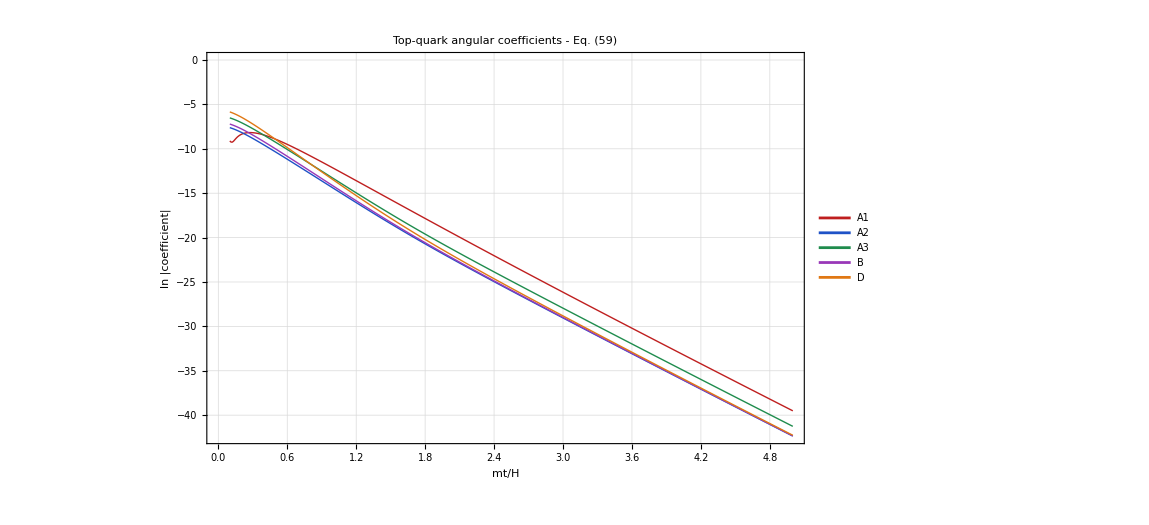

```mathematica
overviewPlotTop=ListLinePlot[Table[logMagnitudeDataTop[j],{j,5}],Frame->True,Axes->False,FrameLabel->{"mt/H","ln |coefficient|"},PlotLabel->"Top-quark angular coefficients - Eq. (59)",PlotLegends->Placed[coefficientNames,Right],PlotStyle->(Directive[#1,Thick]&)/@plotColorsTop,PlotRange->All,ImageSize->850,BaseStyle->{FontFamily->"Times",FontSize->14},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9]]];overviewPlotTop
```

### A1 mass dependence

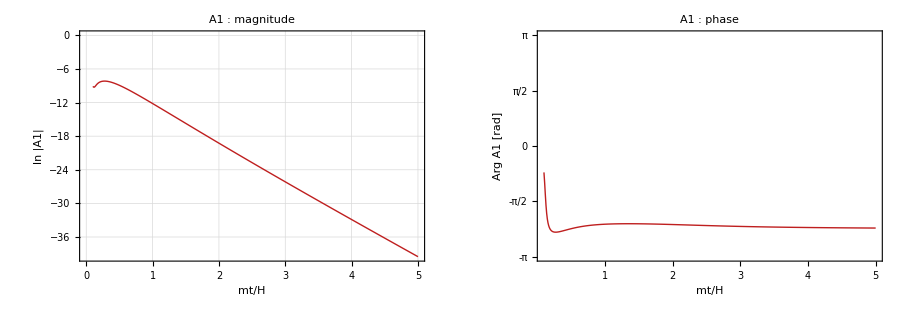

```mathematica
coefficientPlotTop[1]=GraphicsRow[{magnitudePlotTop[1],phasePlotTop[1]},ImageSize->900,Spacings->15];coefficientPlotTop[1]
```

### A2 mass dependence

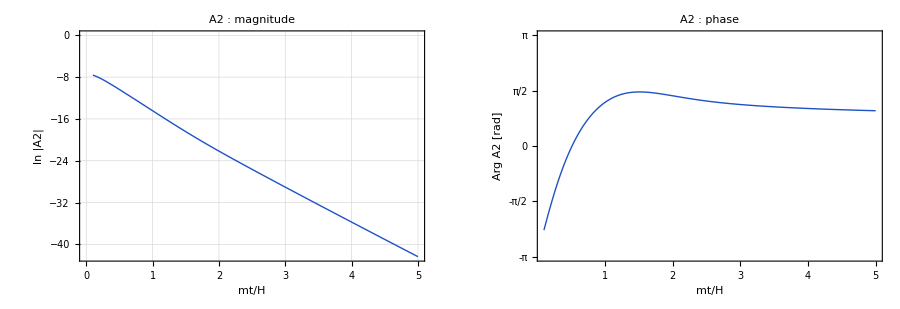

```mathematica
coefficientPlotTop[2]=GraphicsRow[{magnitudePlotTop[2],phasePlotTop[2]},ImageSize->900,Spacings->15];coefficientPlotTop[2]
```

### A3 mass dependence

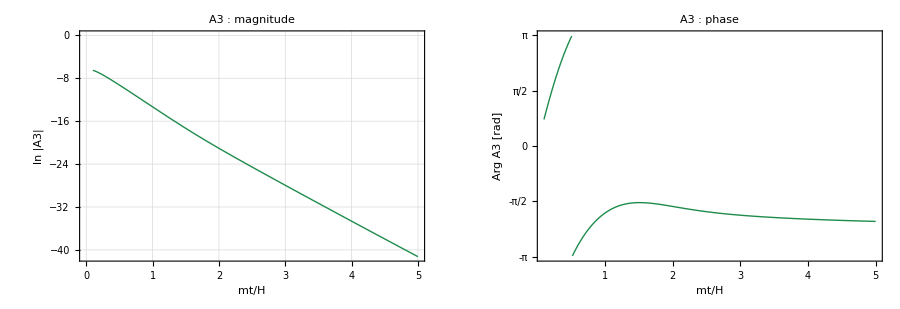

```mathematica
coefficientPlotTop[3]=GraphicsRow[{magnitudePlotTop[3],phasePlotTop[3]},ImageSize->900,Spacings->15];coefficientPlotTop[3]
```

### B mass dependence

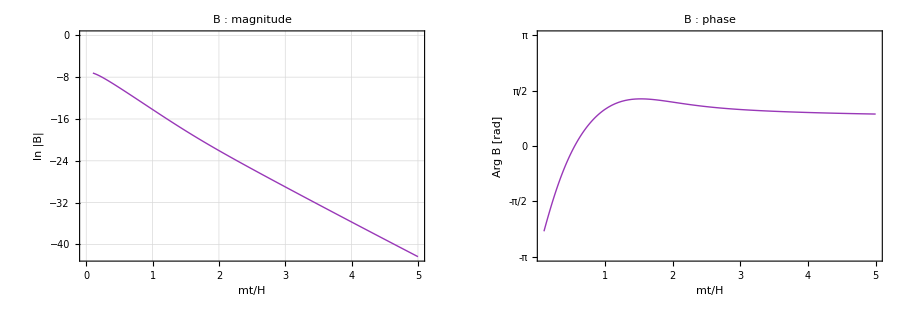

```mathematica
coefficientPlotTop[4]=GraphicsRow[{magnitudePlotTop[4],phasePlotTop[4]},ImageSize->900,Spacings->15];coefficientPlotTop[4]
```

### D mass dependence

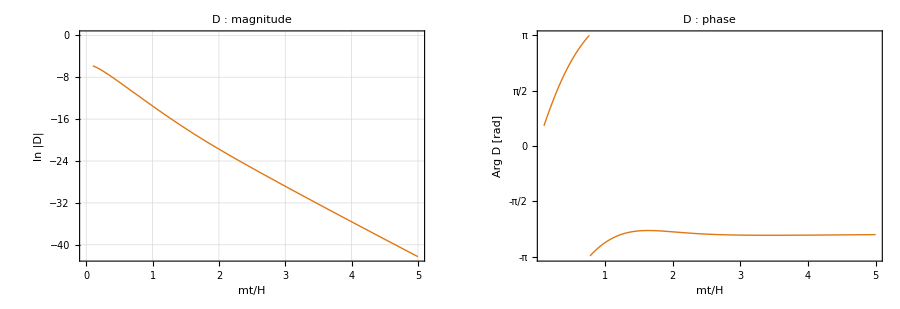

```mathematica
coefficientPlotTop[5]=GraphicsRow[{magnitudePlotTop[5],phasePlotTop[5]},ImageSize->900,Spacings->15];coefficientPlotTop[5]
```

A3 = -3 A2 implies ln|A3| - ln|A2| = ln(3) and a phase difference of Pi modulo 2 Pi. The phase shown is that of each coefficient in the convention of Eq. (58); the phase of the full signal at fixed angles is Arg[Ctop], which also depends on the angular combination.

## 7. Validation summary

These checks validate the implementation of the stated leading collapsed formulas, their algebraic relations, and numerical stability. The regulator comparison is numerical evidence for the finite representation, not a full symbolic proof of that limit or an independent validation of the complete unexpanded fermion box.

```mathematica
validationTop=Association["Soft Gamma normalization"->TrueQ[softGammaCheck==0],"Loop coefficients: symbolic Gamma recurrence"->TrueQ[loopSymbolicCheck==ConstantArray[0,5]],"Loop coefficients: direct Gamma sums"->TrueQ[Max[loopNumericChecks⟦All,2⟧]<1/10^35],"Four Q reductions"->TrueQ[qReductionCheck==ConstantArray[0,4]],"Regulated SK sum vs finite P and H"->TrueQ[Max[Flatten[regulatorChecks⟦All,2;;5⟧]]<1/10^9],"Regulator convergence: four vs five levels"->TrueQ[Max[regulatorChecks⟦All,6⟧]<1/10^9],"Eq. (58) vs angular coefficients"->TrueQ[angularSymbolicCheck==0],"A3 = -3 A2"->TrueQ[a3Check==0],"Precision stability"->TrueQ[Max[precisionChecks⟦All,2⟧]<1/10^25],"Independent angle projections"->TrueQ[Max[Flatten[angularNumericChecks⟦All,2;;4⟧]]<1/10^35],"Mass scan contains finite numeric values"->TrueQ[scanValidTop]];Grid[Prepend[KeyValueMap[{#1,If[#2,Style["PASS",Darker[Green]],Style["FAIL",Red]]}&,validationTop],{"Check","Result"}],Frame->All,Alignment->Left]
```

Check | Result
Soft Gamma normalization | PASS
Loop coefficients: symbolic Gamma recurrence | PASS
Loop coefficients: direct Gamma sums | PASS
Four Q reductions | PASS
Regulated SK sum vs finite P and H | PASS
Regulator convergence: four vs five levels | PASS
Eq. (58) vs angular coefficients | PASS
A3 = -3 A2 | PASS
Precision stability | PASS
Independent angle projections | PASS
Mass scan contains finite numeric values | PASS

```mathematica
EndPackage[];
```